# DM DM -> h2 h2

```mathematica
Quit;
```

```mathematica
ClearAll["Global`*"];
$FeynArtsPath=SetDirectory["~/Work/FeynArts-3.9"]
<<FeynArts`
SetDirectory[$FeynArtsPath<>""]
$FormCalcPath=SetDirectory["~/Work/FormCalc-8.3"]
<<FormCalc`
SetDirectory[$FormCalcPath<>""]
```

/home/anferivera/Work/FeynArts-3.9

FeynArts 3.9 (8 Jul 2015)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

/home/anferivera/Work/FeynArts-3.9

/home/anferivera/Work/FormCalc-8.3

FormCalc 8.3

by Thomas Hahn

last revised 14 Nov 13

/home/anferivera/Work/FormCalc-8.3

## Load the model, choose the topology and the diagram

TopologyList[Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[4][5]],Propagator[Incoming][Vertex[1][2],Vertex[4][5]],Propagator[Outgoing][Vertex[1][3],Vertex[4][5]],Propagator[Outgoing][Vertex[1][4],Vertex[4][5]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][5]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][5]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6]],Propagator[Outgoing][Vertex[1][4],Vertex[3][5]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]]]

loading generic model file /home/anferivera/Work/FeynArts-3.9/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/anferivera/Work/FeynArts-3.9/Models/SDdiracDMEWSB.mod

> 54 particles (incl. antiparticles) in 19 classes

> $CounterTerms are ON

> 112 vertices

classes model {SDdiracDMEWSB} initialized

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 2 Particles insertions

> Top. 4: 2 Particles insertions

in total: 6 Particles insertions

> Top. 1: 2 diagrams

> Top. 2: 2 diagrams

> Top. 3: 2 diagrams

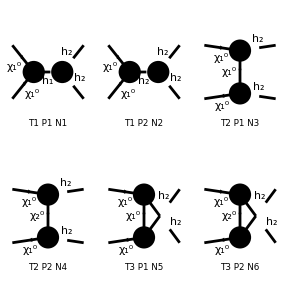

FeynArtsGraphics[{ComposedChar[\chi,1,0],ComposedChar[\chi,1,0]}→{ComposedChar[h,2],ComposedChar[h,2]}][([T1 P1 N1] | [T1 P2 N2] | [T2 P1 N3]
[T2 P2 N4] | [T3 P1 N5] | [T3 P2 N6])]

```mathematica
ClearProcess[];
n22=CreateTopologies[0,2->2]

d22=InsertFields[n22,{F[6,{1}],-F[6,{1}]}->{S[1,{2}],S[1,{2}]}, InsertionLevel->{Particles},Model->"SDdiracDMEWSB",GenericModel->"Lorentz"(*,ExcludeParticles->{S[1,{1}],F[6,{2}] }*) ];
(*d22=InsertFields[n22,{F[6,{1}],-F[6,{1}]}->{V[3],-V[3]}, InsertionLevel->{Particles},Model->"SDdiracDMvsEWSB",GenericModel->"Lorentz"];*)
Paint[d22,ColumnsXRows->{3,2}]
```

> Top. 1: 1 diagram

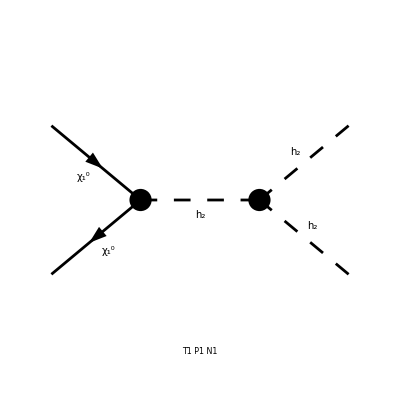

FeynArtsGraphics[{ComposedChar[\chi,1,0],ComposedChar[\chi,1,0]}→{ComposedChar[h,2],ComposedChar[h,2]}][([T1 P1 N1] | Null | Null
Null | Null | Null
Null | Null | Null)]

```mathematica
Paint[d22[[{1}]]]
```

## Amplitude

```mathematica
amp=CreateFeynAmp[d22]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 2 Particles amplitudes

> Top. 3: 2 Particles amplitudes

in total: 6 Particles amplitudes

FeynAmpList[Process→{{F[6,{1}],p1,MassFxv[1],{}},{-F[6,{1}],p2,MassFxv[1],{}}}→{{S[1,{2}],k1,Masshh[2],{}},{S[1,{2}],k2,Masshh[2],{}}},Model→{SDdiracDMEWSB},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{}][FeynAmp[GraphID[Topology==1,Generic==1,Particles==1,Number==1],Integral[],ⅈ v̄[p2,MassFxv[1]].(-(ⅈ XU[1,2]^* om_- (YRD XV[1,1]^* ZH[1,1]+YRC XV[1,2]^* ZH[1,2]))/(√2)-(ⅈ om_+ XU[1,2] (YRD XV[1,1] ZH[1,1]+YRC XV[1,2] ZH[1,2]))/(√2)).u[p1,MassFxv[1]] 1/((k1+k2)^2-Masshh[1]^2) (-ZH[2,2] (LSPH (vS ZH[1,1]+vvSM ZH[1,2]) ZH[2,1]+(LSPH vvSM ZH[1,1]+3 LSP vS ZH[1,2]) ZH[2,2])-ZH[2,1] ((3 Lam vvSM ZH[1,1]+LSPH vS ZH[1,2]) ZH[2,1]+LSPH (vS ZH[1,1]+vvSM ZH[1,2]) ZH[2,2]))],FeynAmp[GraphID[Topology==1,Generic==1,Particles==2,Number==2],Integral[],ⅈ v̄[p2,MassFxv[1]].(-(ⅈ XU[1,2]^* om_- (YRD XV[1,1]^* ZH[2,1]+YRC XV[1,2]^* ZH[2,2]))/(√2)-(ⅈ om_+ XU[1,2] (YRD XV[1,1] ZH[2,1]+YRC XV[1,2] ZH[2,2]))/(√2)).u[p1,MassFxv[1]] 1/((k1+k2)^2-Masshh[2]^2) (-ZH[2,2] (ZH[2,2] (LSPH vvSM ZH[2,1]+3 LSP vS ZH[2,2])+LSPH ZH[2,1] (vS ZH[2,1]+vvSM ZH[2,2]))-ZH[2,1] (ZH[2,1] (3 Lam vvSM ZH[2,1]+LSPH vS ZH[2,2])+LSPH ZH[2,2] (vS ZH[2,1]+vvSM ZH[2,2])))],FeynAmp[GraphID[Topology==2,Generic==1,Particles==1,Number==3],Integral[],v̄[p2,MassFxv[1]].(-(ⅈ XU[1,2]^* om_- (YRD XV[1,1]^* ZH[2,1]+YRC XV[1,2]^* ZH[2,2]))/(√2)-(ⅈ om_+ XU[1,2] (YRD XV[1,1] ZH[2,1]+YRC XV[1,2] ZH[2,2]))/(√2)).(gs[-(p2)+k2]+MassFxv[1]).(-(ⅈ XU[1,2]^* om_- (YRD XV[1,1]^* ZH[2,1]+YRC XV[1,2]^* ZH[2,2]))/(√2)-(ⅈ om_+ XU[1,2] (YRD XV[1,1] ZH[2,1]+YRC XV[1,2] ZH[2,2]))/(√2)).u[p1,MassFxv[1]] 1/((p2-k2)^2-MassFxv[1]^2)],FeynAmp[GraphID[Topology==2,Generic==1,Particles==2,Number==4],Integral[],v̄[p2,MassFxv[1]].(-(ⅈ XU[1,2]^* om_- (YRD XV[2,1]^* ZH[2,1]+YRC XV[2,2]^* ZH[2,2]))/(√2)-(ⅈ om_+ XU[2,2] (YRD XV[1,1] ZH[2,1]+YRC XV[1,2] ZH[2,2]))/(√2)).(gs[-(p2)+k2]+MassFxv[2]).(-(ⅈ XU[2,2]^* om_- (YRD XV[1,1]^* ZH[2,1]+YRC XV[1,2]^* ZH[2,2]))/(√2)-(ⅈ om_+ XU[1,2] (YRD XV[2,1] ZH[2,1]+YRC XV[2,2] ZH[2,2]))/(√2)).u[p1,MassFxv[1]] 1/((p2-k2)^2-MassFxv[2]^2)],FeynAmp[GraphID[Topology==3,Generic==1,Particles==1,Number==5],Integral[],v̄[p2,MassFxv[1]].(-(ⅈ XU[1,2]^* om_- (YRD XV[1,1]^* ZH[2,1]+YRC XV[1,2]^* ZH[2,2]))/(√2)-(ⅈ om_+ XU[1,2] (YRD XV[1,1] ZH[2,1]+YRC XV[1,2] ZH[2,2]))/(√2)).(gs[-(p2)+k1]+MassFxv[1]).(-(ⅈ XU[1,2]^* om_- (YRD XV[1,1]^* ZH[2,1]+YRC XV[1,2]^* ZH[2,2]))/(√2)-(ⅈ om_+ XU[1,2] (YRD XV[1,1] ZH[2,1]+YRC XV[1,2] ZH[2,2]))/(√2)).u[p1,MassFxv[1]] 1/((p2-k1)^2-MassFxv[1]^2)],FeynAmp[GraphID[Topology==3,Generic==1,Particles==2,Number==6],Integral[],v̄[p2,MassFxv[1]].(-(ⅈ XU[1,2]^* om_- (YRD XV[2,1]^* ZH[2,1]+YRC XV[2,2]^* ZH[2,2]))/(√2)-(ⅈ om_+ XU[2,2] (YRD XV[1,1] ZH[2,1]+YRC XV[1,2] ZH[2,2]))/(√2)).(gs[-(p2)+k1]+MassFxv[2]).(-(ⅈ XU[2,2]^* om_- (YRD XV[1,1]^* ZH[2,1]+YRC XV[1,2]^* ZH[2,2]))/(√2)-(ⅈ om_+ XU[1,2] (YRD XV[2,1] ZH[2,1]+YRC XV[2,2] ZH[2,2]))/(√2)).u[p1,MassFxv[1]] 1/((p2-k1)^2-MassFxv[2]^2)]]

```mathematica
resultamp = CalcFeynAmp[amp,FermionChains->VA,FermionOrder->None,  Invariants->True]
```

preparing FORM code in /home/anferivera/Work/FormCalc-8.3/fc-amp-1.frm

running FORM...

ok

Amp[{{F[6,{1}],k[1],MassFxv[1],{}},{-F[6,{1}],k[2],MassFxv[1],{}}}→{{S[1,{2}],k[3],Masshh[2],{}},{S[1,{2}],k[4],Masshh[2],{}}}][(-(1/2 Sub33 Sub6 Den[S,Masshh[1]^2]+3/2 Sub12 Sub8 Den[S,Masshh[2]^2])/(√2)+1/4 (-Sub30 (Den[T,MassFxv[2]^2]+Den[U,MassFxv[2]^2])-Sub14 (Den[T,MassFxv[1]^2]+Den[U,MassFxv[1]^2]) MassFxv[1])) Mat[F1]+(-(1/2 Sub32 Sub6 Den[S,Masshh[1]^2]+3/2 Sub11 Sub8 Den[S,Masshh[2]^2])/(√2)+1/4 (-Sub27 Den[T,MassFxv[2]^2]-Sub22 Den[U,MassFxv[2]^2]-Sub16 (Den[T,MassFxv[1]^2]+Den[U,MassFxv[1]^2]) MassFxv[1])) Mat[F2]-Sub35 (1/4 Den[T,MassFxv[2]^2]-1/4 Den[U,MassFxv[2]^2]) Mat[F4]+Mat[F3] (Sub37 (1/4 Den[T,MassFxv[2]^2]-1/4 Den[U,MassFxv[2]^2])+Sub1 Sub10 XU[1,2]^* (1/2 Den[T,MassFxv[1]^2]-1/2 Den[U,MassFxv[1]^2]) XU[1,2])]

#### Rotation matrices

```mathematica
Den[x_,y_]:=1/(x-y)
expr1=Simplify[ComplexExpand[Plus@@resultamp//.Subexpr[]//.Abbr[]]/.Alfa->e^2/(4Pi)/.{MassFxv[1]->mx1,MassFxv[2]->mx2,Masshh[1]->mh1,Masshh[2]->mh2}/.{ZH[1,1]->Z11,ZH[1,2]->Z12,ZH[2,1]->-Z12,ZH[2,2]->Z11}/.{XV[1,1]->V11,XV[1,2]->V12,XV[2,1]->-V12,XV[2,2]->V11}/.{XU[1,1]->U11,XU[1,2]->U12,XU[2,1]->-U12,XU[2,2]->U11}]
```

1/4 ((mx1 (((2 mx2^2-T-U) U11^2 (V12 YRC Z11-V11 YRD Z12)^2)/((mx2^2-T) (mx2^2-U))+U12^2 (2 (1/(mx2^2-T)+4/(-mx1^2+T)+1/(mx2^2-U)+4/(-mx1^2+U)) V11 V12 YRC YRD Z11 Z12+V11^2 ((1/(mx2^2-T)+1/(mx2^2-U)) YRC^2 Z11^2+4 (1/(mx1^2-T)+1/(mx1^2-U)) YRD^2 Z12^2)+V12^2 (4 (1/(mx1^2-T)+1/(mx1^2-U)) YRC^2 Z11^2+(1/(mx2^2-T)+1/(mx2^2-U)) YRD^2 Z12^2)))+2 U12 (-(mx2 (2 mx2^2-T-U) U11 (V11^2 YRC YRD Z11 Z12-V12^2 YRC YRD Z11 Z12+V11 V12 (-YRC^2 Z11^2+YRD^2 Z12^2)))/((mx2^2-T) (mx2^2-U))-1/((mh2^2-S) (-mh1^2+S))√2 (3 LSP vS Z11^2 (mh2^2 Z12 (V11 YRD Z11+V12 YRC Z12)+mh1^2 Z11 (V12 YRC Z11-V11 YRD Z12)-S V12 YRC (Z11^2+Z12^2))+3 Lam vvSM Z12^2 (mh2^2 Z11 (V11 YRD Z11+V12 YRC Z12)+mh1^2 Z12 (-V12 YRC Z11+V11 YRD Z12)-S V11 YRD (Z11^2+Z12^2))+LSPH (-3 mh1^2 Z11 Z12 (vvSM Z11-vS Z12) (V12 YRC Z11-V11 YRD Z12)-S (Z11^2+Z12^2) (V11 YRD Z11 (vvSM Z11-2 vS Z12)+V12 YRC Z12 (-2 vvSM Z11+vS Z12))+mh2^2 (V11 YRD Z11+V12 YRC Z12) (vS Z12 (-2 Z11^2+Z12^2)+vvSM (Z11^3-2 Z11 Z12^2)))))) Mat[<v2|1|u1>]-(mx1 (T-U) (-U11^2 (V12 YRC Z11-V11 YRD Z12)^2+U12^2 (V11 YRC Z11+V12 YRD Z12)^2) Mat[<v2|5|u1>])/((mx2^2-T) (mx2^2-U))+(U12^2 V11^2 YRC^2 Z11^2 Mat[<v2|1,k[3]|u1>])/(-mx2^2+T)+(U12^2 V11^2 YRC^2 Z11^2 Mat[<v2|1,k[3]|u1>])/(mx2^2-U)+(U11^2 V12^2 YRC^2 Z11^2 Mat[<v2|1,k[3]|u1>])/(-mx2^2+T)+(U11^2 V12^2 YRC^2 Z11^2 Mat[<v2|1,k[3]|u1>])/(mx2^2-U)+(2 U12^2 V12^2 YRC^2 Z11^2 Mat[<v2|1,k[3]|u1>])/(-mx1^2+T)+(2 U12^2 V12^2 YRC^2 Z11^2 Mat[<v2|1,k[3]|u1>])/(mx1^2-U)+(2 U11^2 V11 V12 YRC YRD Z11 Z12 Mat[<v2|1,k[3]|u1>])/(mx2^2-T)+(2 U11^2 V11 V12 YRC YRD Z11 Z12 Mat[<v2|1,k[3]|u1>])/(-mx2^2+U)+(4 U12^2 V11 V12 YRC YRD Z11 Z12 Mat[<v2|1,k[3]|u1>])/(mx1^2-T)+(2 U12^2 V11 V12 YRC YRD Z11 Z12 Mat[<v2|1,k[3]|u1>])/(-mx2^2+T)+(2 U12^2 V11 V12 YRC YRD Z11 Z12 Mat[<v2|1,k[3]|u1>])/(mx2^2-U)+(4 U12^2 V11 V12 YRC YRD Z11 Z12 Mat[<v2|1,k[3]|u1>])/(-mx1^2+U)+(U11^2 V11^2 YRD^2 Z12^2 Mat[<v2|1,k[3]|u1>])/(-mx2^2+T)+(U11^2 V11^2 YRD^2 Z12^2 Mat[<v2|1,k[3]|u1>])/(mx2^2-U)+(2 U12^2 V11^2 YRD^2 Z12^2 Mat[<v2|1,k[3]|u1>])/(-mx1^2+T)+(2 U12^2 V11^2 YRD^2 Z12^2 Mat[<v2|1,k[3]|u1>])/(mx1^2-U)+(U12^2 V12^2 YRD^2 Z12^2 Mat[<v2|1,k[3]|u1>])/(-mx2^2+T)+(U12^2 V12^2 YRD^2 Z12^2 Mat[<v2|1,k[3]|u1>])/(mx2^2-U)+(U12^2 V11^2 YRC^2 Z11^2 Mat[<v2|5,k[3]|u1>])/(mx2^2-T)+(U12^2 V11^2 YRC^2 Z11^2 Mat[<v2|5,k[3]|u1>])/(-mx2^2+U)+(U11^2 V12^2 YRC^2 Z11^2 Mat[<v2|5,k[3]|u1>])/(-mx2^2+T)+(U11^2 V12^2 YRC^2 Z11^2 Mat[<v2|5,k[3]|u1>])/(mx2^2-U)+(2 U11^2 V11 V12 YRC YRD Z11 Z12 Mat[<v2|5,k[3]|u1>])/(mx2^2-T)+(2 U11^2 V11 V12 YRC YRD Z11 Z12 Mat[<v2|5,k[3]|u1>])/(-mx2^2+U)+(2 U12^2 V11 V12 YRC YRD Z11 Z12 Mat[<v2|5,k[3]|u1>])/(mx2^2-T)+(2 U12^2 V11 V12 YRC YRD Z11 Z12 Mat[<v2|5,k[3]|u1>])/(-mx2^2+U)+(U11^2 V11^2 YRD^2 Z12^2 Mat[<v2|5,k[3]|u1>])/(-mx2^2+T)+(U11^2 V11^2 YRD^2 Z12^2 Mat[<v2|5,k[3]|u1>])/(mx2^2-U)+(U12^2 V12^2 YRD^2 Z12^2 Mat[<v2|5,k[3]|u1>])/(mx2^2-T)+(U12^2 V12^2 YRD^2 Z12^2 Mat[<v2|5,k[3]|u1>])/(-mx2^2+U))

#### Kine of Dirac Chains in the AMPLITUDE

```mathematica
InputForm[expr1/.{Mat[DiracChain[Spinor[k[2],mx1,-1],1,Spinor[k[1],mx1,1]]]->0,
Mat[DiracChain[Spinor[k[2],mx1,-1],5,Spinor[k[1],mx1,1]]]->0,
Mat[DiracChain[Spinor[k[2],mx1,-1],1,k[3],Spinor[k[1],mx1,1]]]->0,
Mat[DiracChain[Spinor[k[2],mx1,-1],5,k[3],Spinor[k[1],mx1,1]]]->0}]
```

0

```mathematica
expr1/.{Mat[DiracChain[Spinor[k[2],mx1,-1],1,Spinor[k[1],mx1,1]]]->F1,
Mat[DiracChain[Spinor[k[2],mx1,-1],5,Spinor[k[1],mx1,1]]]->F5,
Mat[DiracChain[Spinor[k[2],mx1,-1],1,k[3],Spinor[k[1],mx1,1]]]->F13,
Mat[DiracChain[Spinor[k[2],mx1,-1],5,k[3],Spinor[k[1],mx1,1]]]->F53}
```

```mathematica
expr2 = Simplify[expr1/.{Mat[DiracChain[Spinor[k[2],mx1,-1],1,Spinor[k[1],mx1,1]]]->F1,
Mat[DiracChain[Spinor[k[2],mx1,-1],5,Spinor[k[1],mx1,1]]]->F5,
Mat[DiracChain[Spinor[k[2],mx1,-1],1,k[3],Spinor[k[1],mx1,1]]]->F13,
Mat[DiracChain[Spinor[k[2],mx1,-1],5,k[3],Spinor[k[1],mx1,1]]]->F53}]
```

1/4 ((F53 U12^2 V11^2 YRC^2 Z11^2)/(mx2^2-T)+(F13 U12^2 V11^2 YRC^2 Z11^2)/(-mx2^2+T)+(F13 U12^2 V11^2 YRC^2 Z11^2)/(mx2^2-U)+(F53 U12^2 V11^2 YRC^2 Z11^2)/(-mx2^2+U)+(F13 U11^2 V12^2 YRC^2 Z11^2)/(-mx2^2+T)+(F53 U11^2 V12^2 YRC^2 Z11^2)/(-mx2^2+T)+(F13 U11^2 V12^2 YRC^2 Z11^2)/(mx2^2-U)+(F53 U11^2 V12^2 YRC^2 Z11^2)/(mx2^2-U)+(2 F13 U12^2 V12^2 YRC^2 Z11^2)/(-mx1^2+T)+(2 F13 U12^2 V12^2 YRC^2 Z11^2)/(mx1^2-U)+(2 F13 U11^2 V11 V12 YRC YRD Z11 Z12)/(mx2^2-T)+(2 F53 U11^2 V11 V12 YRC YRD Z11 Z12)/(mx2^2-T)+(2 F13 U11^2 V11 V12 YRC YRD Z11 Z12)/(-mx2^2+U)+(2 F53 U11^2 V11 V12 YRC YRD Z11 Z12)/(-mx2^2+U)+(4 F13 U12^2 V11 V12 YRC YRD Z11 Z12)/(mx1^2-T)+(2 F53 U12^2 V11 V12 YRC YRD Z11 Z12)/(mx2^2-T)+(2 F13 U12^2 V11 V12 YRC YRD Z11 Z12)/(-mx2^2+T)+(2 F13 U12^2 V11 V12 YRC YRD Z11 Z12)/(mx2^2-U)+(4 F13 U12^2 V11 V12 YRC YRD Z11 Z12)/(-mx1^2+U)+(2 F53 U12^2 V11 V12 YRC YRD Z11 Z12)/(-mx2^2+U)+(F13 U11^2 V11^2 YRD^2 Z12^2)/(-mx2^2+T)+(F53 U11^2 V11^2 YRD^2 Z12^2)/(-mx2^2+T)+(F13 U11^2 V11^2 YRD^2 Z12^2)/(mx2^2-U)+(F53 U11^2 V11^2 YRD^2 Z12^2)/(mx2^2-U)+(2 F13 U12^2 V11^2 YRD^2 Z12^2)/(-mx1^2+T)+(2 F13 U12^2 V11^2 YRD^2 Z12^2)/(mx1^2-U)+(F53 U12^2 V12^2 YRD^2 Z12^2)/(mx2^2-T)+(F13 U12^2 V12^2 YRD^2 Z12^2)/(-mx2^2+T)+(F13 U12^2 V12^2 YRD^2 Z12^2)/(mx2^2-U)+(F53 U12^2 V12^2 YRD^2 Z12^2)/(-mx2^2+U)-(F5 mx1 (T-U) (-U11^2 (V12 YRC Z11-V11 YRD Z12)^2+U12^2 (V11 YRC Z11+V12 YRD Z12)^2))/((mx2^2-T) (mx2^2-U))+F1 (mx1 (((2 mx2^2-T-U) U11^2 (V12 YRC Z11-V11 YRD Z12)^2)/((mx2^2-T) (mx2^2-U))+U12^2 (2 (1/(mx2^2-T)+4/(-mx1^2+T)+1/(mx2^2-U)+4/(-mx1^2+U)) V11 V12 YRC YRD Z11 Z12+V11^2 ((1/(mx2^2-T)+1/(mx2^2-U)) YRC^2 Z11^2+4 (1/(mx1^2-T)+1/(mx1^2-U)) YRD^2 Z12^2)+V12^2 (4 (1/(mx1^2-T)+1/(mx1^2-U)) YRC^2 Z11^2+(1/(mx2^2-T)+1/(mx2^2-U)) YRD^2 Z12^2)))+2 U12 (-(mx2 (2 mx2^2-T-U) U11 (V11^2 YRC YRD Z11 Z12-V12^2 YRC YRD Z11 Z12+V11 V12 (-YRC^2 Z11^2+YRD^2 Z12^2)))/((mx2^2-T) (mx2^2-U))-1/((mh2^2-S) (-mh1^2+S))√2 (3 LSP vS Z11^2 (mh2^2 Z12 (V11 YRD Z11+V12 YRC Z12)+mh1^2 Z11 (V12 YRC Z11-V11 YRD Z12)-S V12 YRC (Z11^2+Z12^2))+3 Lam vvSM Z12^2 (mh2^2 Z11 (V11 YRD Z11+V12 YRC Z12)+mh1^2 Z12 (-V12 YRC Z11+V11 YRD Z12)-S V11 YRD (Z11^2+Z12^2))+LSPH (-3 mh1^2 Z11 Z12 (vvSM Z11-vS Z12) (V12 YRC Z11-V11 YRD Z12)-S (Z11^2+Z12^2) (V11 YRD Z11 (vvSM Z11-2 vS Z12)+V12 YRC Z12 (-2 vvSM Z11+vS Z12))+mh2^2 (V11 YRD Z11+V12 YRC Z12) (vS Z12 (-2 Z11^2+Z12^2)+vvSM (Z11^3-2 Z11 Z12^2)))))))

#### Factors in the AMPLITUDE

```mathematica
M1=Simplify[D[expr2,F1]]
```

1/4 (mx1 (((2 mx2^2-T-U) U11^2 (V12 YRC Z11-V11 YRD Z12)^2)/((mx2^2-T) (mx2^2-U))+U12^2 (2 (1/(mx2^2-T)+4/(-mx1^2+T)+1/(mx2^2-U)+4/(-mx1^2+U)) V11 V12 YRC YRD Z11 Z12+V11^2 ((1/(mx2^2-T)+1/(mx2^2-U)) YRC^2 Z11^2+4 (1/(mx1^2-T)+1/(mx1^2-U)) YRD^2 Z12^2)+V12^2 (4 (1/(mx1^2-T)+1/(mx1^2-U)) YRC^2 Z11^2+(1/(mx2^2-T)+1/(mx2^2-U)) YRD^2 Z12^2)))+2 U12 (-(mx2 (2 mx2^2-T-U) U11 (V11^2 YRC YRD Z11 Z12-V12^2 YRC YRD Z11 Z12+V11 V12 (-YRC^2 Z11^2+YRD^2 Z12^2)))/((mx2^2-T) (mx2^2-U))-1/((mh2^2-S) (-mh1^2+S))√2 (3 LSP vS Z11^2 (mh2^2 Z12 (V11 YRD Z11+V12 YRC Z12)+mh1^2 Z11 (V12 YRC Z11-V11 YRD Z12)-S V12 YRC (Z11^2+Z12^2))+3 Lam vvSM Z12^2 (mh2^2 Z11 (V11 YRD Z11+V12 YRC Z12)+mh1^2 Z12 (-V12 YRC Z11+V11 YRD Z12)-S V11 YRD (Z11^2+Z12^2))+LSPH (-3 mh1^2 Z11 Z12 (vvSM Z11-vS Z12) (V12 YRC Z11-V11 YRD Z12)-S (Z11^2+Z12^2) (V11 YRD Z11 (vvSM Z11-2 vS Z12)+V12 YRC Z12 (-2 vvSM Z11+vS Z12))+mh2^2 (V11 YRD Z11+V12 YRC Z12) (vS Z12 (-2 Z11^2+Z12^2)+vvSM (Z11^3-2 Z11 Z12^2))))))

```mathematica
M2=Simplify[D[expr2,F5]]
```

-(mx1 (T-U) (-U11^2 (V12 YRC Z11-V11 YRD Z12)^2+U12^2 (V11 YRC Z11+V12 YRD Z12)^2))/(4 (mx2^2-T) (mx2^2-U))

```mathematica
M3=Simplify[D[expr2,F13]]
```

1/4 (-((T-U) U11^2 (V12 YRC Z11-V11 YRD Z12)^2)/((mx2^2-T) (mx2^2-U))+U12^2 (2 (2/(mx1^2-T)+1/(-mx2^2+T)+1/(mx2^2-U)+2/(-mx1^2+U)) V11 V12 YRC YRD Z11 Z12+V12^2 (-(2 (T-U) YRC^2 Z11^2)/((mx1^2-T) (mx1^2-U))+(1/(-mx2^2+T)+1/(mx2^2-U)) YRD^2 Z12^2)+V11^2 ((1/(-mx2^2+T)+1/(mx2^2-U)) YRC^2 Z11^2+(2 (-T+U) YRD^2 Z12^2)/((mx1^2-T) (mx1^2-U)))))

```mathematica
M4=Simplify[D[expr2,F53]]
```

((T-U) (-U11^2 (V12 YRC Z11-V11 YRD Z12)^2+U12^2 (V11 YRC Z11+V12 YRD Z12)^2))/(4 (mx2^2-T) (mx2^2-U))

#### Factorization of the Amplitude

```mathematica
expr3 =(M1*F1+M2*F5+M3*F13+M4*F53);
```

```mathematica
Simplify[expr2 -expr3]
```

0

## Momenta in the computation for the CM frame

```mathematica
kinematic=Solve[{E1==1/2*Sqrt[S]&&p1==Sqrt[E1^2-Me^2]},{E1,p1}][[1]]
```

{E1→(√S)/2,p1→1/2 √(-4 Me^2+S)}

In two dimensions...

```mathematica
k1={E1,p1,0,0};
k2={E1,-p1,0,0};
k3={E1,p2*ct,p2*st,0}/.st->Sqrt[1-ct^2];
k4={E1,-p2*ct,-p2*st,0}/.st->Sqrt[1-ct^2];
```

Mandelstan variables

```mathematica
guv = {{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}};
MatrixForm[guv]
```

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

```mathematica
MV = Simplify[{S->(k1 + k2).guv.(k1 + k2),   
		         T->(k1 - k3).guv.(k1 - k3),   
                            U ->(k1 - k4).guv.(k1 - k4)}]
```

{S→4 E1^2,T→-p1^2+2 ct p1 p2-p2^2,U→-p1^2-2 ct p1 p2-p2^2}

## Dirac spinors and Gamma matrices

Dirac matrices

```mathematica
gamma0={{1,0,0,0},{0,1,0,0},{0,0,-1,0},{0,0,0,-1}};
gamma1={{0,0,0,1},{0,0,1,0},{0,-1,0,0},{-1,0,0,0}};
gamma2={{0,0,0,-I},{0,0,I,0},{0,I,0,0},{-I,0,0,0}};
gamma3={{0,0,1,0},{0,0,0,-1},{-1,0,0,0},{0,1,0,0}};

gamma5={{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}};
gammamu={gamma0,gamma1,gamma2,gamma3,gamma5};
```

```mathematica
Grid[{{"γ0","γ1","γ2","γ3","γ5"},{gamma0//MatrixForm,gamma1//MatrixForm,gamma2//MatrixForm,gamma3//MatrixForm,gamma5//MatrixForm}},Frame->All]
```

γ0 | γ1 | γ2 | γ3 | γ5
(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1) | (0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0) | (0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0) | (0 | 0 | 1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0) | (0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)

Check properties of gamma matrices ...

```mathematica
Dot[gamma0,gamma0]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

[γu,γv]=2guv

```mathematica
Grid[{{"i=0","i=1","i=2","i=3"},{ Simplify[Sum[(Dot[i,j]+Dot[j,i]),{i,{gamma0}},{j,{gamma0}}]]//MatrixForm,Simplify[Sum[(Dot[i,j]+Dot[j,i]),{i,{gamma1}},{j,{gamma1}}]]//MatrixForm,Simplify[Sum[(Dot[i,j]+Dot[j,i]),{i,{gamma2}},{j,{gamma2}}]] //MatrixForm ,Simplify[Sum[(Dot[i,j]+Dot[j,i]),{i,{gamma3}},{j,{gamma3}}]]//MatrixForm} },Frame->All]
```

i=0 | i=1 | i=2 | i=3
(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 2) | (-2 | 0 | 0 | 0
0 | -2 | 0 | 0
0 | 0 | -2 | 0
0 | 0 | 0 | -2) | (-2 | 0 | 0 | 0
0 | -2 | 0 | 0
0 | 0 | -2 | 0
0 | 0 | 0 | -2) | (-2 | 0 | 0 | 0
0 | -2 | 0 | 0
0 | 0 | -2 | 0
0 | 0 | 0 | -2)

```mathematica
χ[s_]:=If[s==1,{1,0},{0,1}]
Grid[{{χ1,χ2},{χ[1]//MatrixForm,χ[-1]//MatrixForm}},Frame->All]
```

χ1 | χ2
(1
0) | (0
1)

Spinors (Cheng appendix)

```mathematica
σp1=((Total[k1[[#+1]] PauliMatrix[#]&/@Range[3]])/(k1[[1]]+mx1));
σp2=((Total[k2[[#+1]] PauliMatrix[#]&/@Range[3]])/(k2[[1]]+mx1));
σp3=((Total[k3[[#+1]] PauliMatrix[#]&/@Range[3]])/(k3[[1]]+mx1));
σp4=((Total[k4[[#+1]] PauliMatrix[#]&/@Range[3]])/(k4[[1]]+mx1));
```

```mathematica
uspinor[s_,eif_,mif_,ki_]:=Sqrt[ki+mif] ArrayFlatten[{χ[s],Dot[eif,χ[s]]},1]
uspinor[1,σp2,mx1,k2[[1]]]
```

{√(E1+mx1),0,0,-p1/(√(E1+mx1))}

```mathematica
vspinor[s_,eif_,mif_,ki_]:=Sqrt[ki+mif] ArrayFlatten[{Dot[eif,χ[s]],χ[s]},1]
vspinor[1,σp2,mx1,k2[[1]]]
```

{0,-p1/(√(E1+mx1)),√(E1+mx1),0}

Check normalization for the U Spinors (input and output)

```mathematica
Simplify[Simplify[Simplify[(Conjugate[uspinor[1,σp1,mx1,k1[[1]]]]).gamma0.uspinor[1,σp1,mx1,k1[[1]]]/.{S->4E1^2}],Element[{E1,mx1,√(E1+mx1),1/(√(E1+mx1)),p1},Reals] ]/.{p1^2-> E1^2-mx1^2}]
Simplify[Simplify[Simplify[(Conjugate[uspinor[1,σp2,mx1,k2[[1]]]]).gamma0.uspinor[1,σp2,mx1,k2[[1]]]/.{S->4E1^2}],Element[{E1,mx1,√(E1+mx1),1/(√(E1+mx1)),p1},Reals] ]/.{p1^2-> E1^2-mx1^2}];
Simplify[Simplify[(Conjugate[uspinor[1,σp3,mx1,k3[[1]]]]).gamma0.uspinor[1,σp3,mx1,k3[[1]]],Element[{ct,st,p1,mx1,E1,1/(√(E1+mx1)),√(E1+mx1),√(1-ct^2)},Reals]]/.{p1^2-> E1^2-mx1^2,st->Sqrt[1-ct^2]}];
Simplify[Simplify[(Conjugate[uspinor[1,σp4,mx1,k4[[1]]]]).gamma0.uspinor[1,σp4,mx1,k4[[1]]],Element[{ct,st,p1,mx1,E1,1/(√(E1+mx1)),√(E1+mx1),√(1-ct^2)},Reals]]/.{(ct^2+st^2)->1,p1^2-> E1^2-mx1^2}];
```

2 mx1

Check normalization for the V Spinors

```mathematica
Simplify[Simplify[Simplify[(Conjugate[vspinor[1,σp1,Me,k1[[1]]]]).gamma0.vspinor[1,σp1,Me,k1[[1]]]/.{S->4E1^2}],Element[{E1,Me,√(E1+Me),1/(√(E1+Me)),p1},Reals] ]/.{p1^2-> E1^2-Me^2}]
Simplify[Simplify[Simplify[(Conjugate[vspinor[1,σp2,Me,k2[[1]]]]).gamma0.vspinor[1,σp2,Me,k2[[1]]]/.{S->4E1^2}],Element[{E1,Me,√(E1+Me),1/(√(E1+Me)),p1},Reals] ]/.{p1^2-> E1^2-Me^2}];
Simplify[Simplify[(Conjugate[vspinor[1,σp3,Me,k3[[1]]]]).gamma0.vspinor[1,σp3,Me,k3[[1]]],Element[{ct,st,p1,Me,E1,1/(√(E1+Me)),√(E1+Me),√(1-ct^2)},Reals]]/.{p1^2-> E1^2-Me^2,st->Sqrt[1-ct^2]}];
Simplify[Simplify[(Conjugate[vspinor[1,σp4,Me,k4[[1]]]]).gamma0.vspinor[1,σp4,Me,k4[[1]]],Element[{ct,st,p1,Me,E1,1/(√(E1+Me)),√(E1+Me),√(1-ct^2)},Reals]]/.{(ct^2+st^2)->1,p1^2-> E1^2-Me^2}];
```

-2 Me

(OverBar[U1]γaU2)^†=(OverBar[U2]γaU1)

```mathematica
AA1=(Conjugate[uspinor[1,σp1,Me,k1[[1]]]]).gamma0.gamma2.uspinor[1,σp3,Me,k3[[1]]]
AA2=(Conjugate[uspinor[1,σp3,Me,k3[[1]]]]).gamma0.gamma2.uspinor[1,σp1,Me,k1[[1]]]
Simplify[Conjugate[AA1]-AA2]
```

-(ⅈ (ct p2+ⅈ √(1-ct^2) p2) (√(E1+Me))^*)/(√(E1+Me))+ⅈ √(E1+Me) (1/(√(E1+Me)))^* p1^*

-(ⅈ p1 (√(E1+Me))^*)/(√(E1+Me))+ⅈ √(E1+Me) (1/(√(E1+Me)))^* (ct^* p2^*-ⅈ (√(1-ct^2))^* p2^*)

0

```mathematica
BB1=(Conjugate[vspinor[1,σp1,Me,k1[[1]]]]).gamma0.gamma2.vspinor[1,σp4,Me,k3[[1]]]
BB2=(Conjugate[vspinor[1,σp4,Me,k3[[1]]]]).gamma0.gamma2.vspinor[1,σp1,Me,k1[[1]]]
Simplify[Conjugate[BB1]-BB2]
```

-(ⅈ (-ct p2-ⅈ √(1-ct^2) p2) (√(E1+Me))^*)/(√(E1+Me))+ⅈ √(E1+Me) (1/(√(E1+Me)))^* p1^*

-(ⅈ p1 (√(E1+Me))^*)/(√(E1+Me))+ⅈ √(E1+Me) (1/(√(E1+Me)))^* (-ct^* p2^*+ⅈ (√(1-ct^2))^* p2^*)

0

## Amplitude square

Manipulation of the amplitude

BB Function : Square of the amplitude. I translated the Dirac Chain to the common notation in terms of Dirac spinors

```mathematica
expr3
```

(F53 (T-U) (-U11^2 (V12 YRC Z11-V11 YRD Z12)^2+U12^2 (V11 YRC Z11+V12 YRD Z12)^2))/(4 (mx2^2-T) (mx2^2-U))-(F5 mx1 (T-U) (-U11^2 (V12 YRC Z11-V11 YRD Z12)^2+U12^2 (V11 YRC Z11+V12 YRD Z12)^2))/(4 (mx2^2-T) (mx2^2-U))+1/4 F13 (-((T-U) U11^2 (V12 YRC Z11-V11 YRD Z12)^2)/((mx2^2-T) (mx2^2-U))+U12^2 (2 (2/(mx1^2-T)+1/(-mx2^2+T)+1/(mx2^2-U)+2/(-mx1^2+U)) V11 V12 YRC YRD Z11 Z12+V12^2 (-(2 (T-U) YRC^2 Z11^2)/((mx1^2-T) (mx1^2-U))+(1/(-mx2^2+T)+1/(mx2^2-U)) YRD^2 Z12^2)+V11^2 ((1/(-mx2^2+T)+1/(mx2^2-U)) YRC^2 Z11^2+(2 (-T+U) YRD^2 Z12^2)/((mx1^2-T) (mx1^2-U)))))+1/4 F1 (mx1 (((2 mx2^2-T-U) U11^2 (V12 YRC Z11-V11 YRD Z12)^2)/((mx2^2-T) (mx2^2-U))+U12^2 (2 (1/(mx2^2-T)+4/(-mx1^2+T)+1/(mx2^2-U)+4/(-mx1^2+U)) V11 V12 YRC YRD Z11 Z12+V11^2 ((1/(mx2^2-T)+1/(mx2^2-U)) YRC^2 Z11^2+4 (1/(mx1^2-T)+1/(mx1^2-U)) YRD^2 Z12^2)+V12^2 (4 (1/(mx1^2-T)+1/(mx1^2-U)) YRC^2 Z11^2+(1/(mx2^2-T)+1/(mx2^2-U)) YRD^2 Z12^2)))+2 U12 (-(mx2 (2 mx2^2-T-U) U11 (V11^2 YRC YRD Z11 Z12-V12^2 YRC YRD Z11 Z12+V11 V12 (-YRC^2 Z11^2+YRD^2 Z12^2)))/((mx2^2-T) (mx2^2-U))-1/((mh2^2-S) (-mh1^2+S))√2 (3 LSP vS Z11^2 (mh2^2 Z12 (V11 YRD Z11+V12 YRC Z12)+mh1^2 Z11 (V12 YRC Z11-V11 YRD Z12)-S V12 YRC (Z11^2+Z12^2))+3 Lam vvSM Z12^2 (mh2^2 Z11 (V11 YRD Z11+V12 YRC Z12)+mh1^2 Z12 (-V12 YRC Z11+V11 YRD Z12)-S V11 YRD (Z11^2+Z12^2))+LSPH (-3 mh1^2 Z11 Z12 (vvSM Z11-vS Z12) (V12 YRC Z11-V11 YRD Z12)-S (Z11^2+Z12^2) (V11 YRD Z11 (vvSM Z11-2 vS Z12)+V12 YRC Z12 (-2 vvSM Z11+vS Z12))+mh2^2 (V11 YRD Z11+V12 YRC Z12) (vS Z12 (-2 Z11^2+Z12^2)+vvSM (Z11^3-2 Z11 Z12^2))))))

#### Dirac Chains in the amplitude (F1,F5,F13,F53)

```mathematica
Mat[DiracChain[Spinor[k[2],mx1,-1],1,Spinor[k[1],mx1,1]]]
Mat[DiracChain[Spinor[k[2],mx1,-1],5,Spinor[k[1],mx1,1]]]
Mat[DiracChain[Spinor[k[2],mx1,-1],1,k[3],Spinor[k[1],mx1,1]]]
Mat[DiracChain[Spinor[k[2],mx1,-1],5,k[3],Spinor[k[1],mx1,1]]]
```

Mat[<v2|1|u1>]

Mat[<v2|5|u1>]

Mat[<v2|1,k[3]|u1>]

Mat[<v2|5,k[3]|u1>]

```mathematica
AMP[s1_,s2_]:=expr3//.{
F1->Dot[(Conjugate[vspinor[s2,σp2,mx1,k2[[1]]]]).Dot[gamma0,IdentityMatrix[4]],uspinor[s1,σp1,mx1,k1[[1]]]],
F5->Dot[(Conjugate[vspinor[s2,σp2,mx1,k2[[1]]]]).Dot[gamma0,gamma5],uspinor[s1,σp1,mx1,k1[[1]]]],
F13->Dot[(Conjugate[vspinor[s2,σp2,mx1,k2[[1]]]]).Dot[gamma0,(k3[[1]]*gamma0+k3[[2]]*gamma1+k3[[3]]*gamma2+k3[[4]]*gamma3)],uspinor[s1,σp1,mx1,k1[[1]]]],
F53->Dot[(Conjugate[vspinor[s2,σp2,mx1,k2[[1]]]]).Dot[gamma0,gamma5,(k3[[1]]*gamma0+k3[[2]]*gamma1+k3[[3]]*gamma2+k3[[4]]*gamma3)],uspinor[s1,σp1,mx1,k1[[1]]]]
}
```

```mathematica
AMP[-1,1]
```

1/4 (mx1 (((2 mx2^2-T-U) U11^2 (V12 YRC Z11-V11 YRD Z12)^2)/((mx2^2-T) (mx2^2-U))+U12^2 (2 (1/(mx2^2-T)+4/(-mx1^2+T)+1/(mx2^2-U)+4/(-mx1^2+U)) V11 V12 YRC YRD Z11 Z12+V11^2 ((1/(mx2^2-T)+1/(mx2^2-U)) YRC^2 Z11^2+4 (1/(mx1^2-T)+1/(mx1^2-U)) YRD^2 Z12^2)+V12^2 (4 (1/(mx1^2-T)+1/(mx1^2-U)) YRC^2 Z11^2+(1/(mx2^2-T)+1/(mx2^2-U)) YRD^2 Z12^2)))+2 U12 (-(mx2 (2 mx2^2-T-U) U11 (V11^2 YRC YRD Z11 Z12-V12^2 YRC YRD Z11 Z12+V11 V12 (-YRC^2 Z11^2+YRD^2 Z12^2)))/((mx2^2-T) (mx2^2-U))-1/((mh2^2-S) (-mh1^2+S))√2 (3 LSP vS Z11^2 (mh2^2 Z12 (V11 YRD Z11+V12 YRC Z12)+mh1^2 Z11 (V12 YRC Z11-V11 YRD Z12)-S V12 YRC (Z11^2+Z12^2))+3 Lam vvSM Z12^2 (mh2^2 Z11 (V11 YRD Z11+V12 YRC Z12)+mh1^2 Z12 (-V12 YRC Z11+V11 YRD Z12)-S V11 YRD (Z11^2+Z12^2))+LSPH (-3 mh1^2 Z11 Z12 (vvSM Z11-vS Z12) (V12 YRC Z11-V11 YRD Z12)-S (Z11^2+Z12^2) (V11 YRD Z11 (vvSM Z11-2 vS Z12)+V12 YRC Z12 (-2 vvSM Z11+vS Z12))+mh2^2 (V11 YRD Z11+V12 YRC Z12) (vS Z12 (-2 Z11^2+Z12^2)+vvSM (Z11^3-2 Z11 Z12^2)))))) (-(p1 (√(E1+mx1))^*)/(√(E1+mx1))-√(E1+mx1) (1/(√(E1+mx1)))^* p1^*)+1/4 (-((T-U) U11^2 (V12 YRC Z11-V11 YRD Z12)^2)/((mx2^2-T) (mx2^2-U))+U12^2 (2 (2/(mx1^2-T)+1/(-mx2^2+T)+1/(mx2^2-U)+2/(-mx1^2+U)) V11 V12 YRC YRD Z11 Z12+V12^2 (-(2 (T-U) YRC^2 Z11^2)/((mx1^2-T) (mx1^2-U))+(1/(-mx2^2+T)+1/(mx2^2-U)) YRD^2 Z12^2)+V11^2 ((1/(-mx2^2+T)+1/(mx2^2-U)) YRC^2 Z11^2+(2 (-T+U) YRD^2 Z12^2)/((mx1^2-T) (mx1^2-U))))) (√(E1+mx1) ((ct p2-ⅈ √(1-ct^2) p2) (√(E1+mx1))^*-E1 (1/(√(E1+mx1)))^* p1^*)+(p1 (E1 (√(E1+mx1))^*-(ct p2+ⅈ √(1-ct^2) p2) (1/(√(E1+mx1)))^* p1^*))/(√(E1+mx1)))

Sum over spinors and gamma matrices.. trick! Warning: I do the gamma matrices explicitly because i need to avoid the index in the gamma_uv.

```mathematica
Clear[AMP2]
```

```mathematica
AMP2=(1/4)*Simplify[(Simplify[Sum[AMP[s1,s2,s3,s4,g1]*Conjugate[AMP[s1,s2,s3,s4,g2]],{s1,{1,-1}},{s2,{1,-1}},{s3,{1,-1}},{s4,{1,-1}},{g1,{gamma0}},{g2,{gamma0}}],Element[{1/(√(E1+Me)),√(E1+Me),p1,Me,ct,√(1-ct^2),e},Reals]]-Simplify[Sum[AMP[s1,s2,s3,s4,g1]*Conjugate[AMP[s1,s2,s3,s4,g2]],{s1,{1,-1}},{s2,{1,-1}},{s3,{1,-1}},{s4,{1,-1}},{g1,{gamma0}},{g2,{gamma1,gamma2,gamma3}}],Element[{1/(√(E1+Me)),√(E1+Me),p1,Me,ct,√(1-ct^2),e},Reals]]-Simplify[Sum[AMP[s1,s2,s3,s4,g1]*Conjugate[AMP[s1,s2,s3,s4,g2]],{s1,{1,-1}},{s2,{1,-1}},{s3,{1,-1}},{s4,{1,-1}},{g1,{gamma1,gamma2,gamma3}},{g2,{gamma0}}],Element[{1/(√(E1+Me)),√(E1+Me),p1,Me,ct,√(1-ct^2),e},Reals]]+Simplify[Sum[AMP[s1,s2,s3,s4,g1]*Conjugate[AMP[s1,s2,s3,s4,g2]],{s1,{1,-1}},{s2,{1,-1}},{s3,{1,-1}},{s4,{1,-1}},{g1,{gamma1,gamma2,gamma3}},{g2,{gamma1,gamma2,gamma3}}],Element[{1/(√(E1+Me)),√(E1+Me),p1,Me,ct,√(1-ct^2),e},Reals]])]
```

1/((E1+Me)^4 T^2 U^2)e^4 (E1^8 (T^2-T U+U^2)+8 E1^7 Me (T^2-T U+U^2)+Me^8 (T^2-T U+U^2)+p1^8 (T^2-T U+U^2)+4 Me^6 p1^2 ((1-2 ct) T^2+T U+(1+2 ct) U^2)+4 Me^2 p1^6 ((1-2 ct) T^2+T U+(1+2 ct) U^2)+2 Me^4 p1^4 ((15+4 ct^2) T^2+29 T U+(15+4 ct^2) U^2)+4 E1^6 (7 Me^2 (T^2-T U+U^2)+p1^2 (T^2-2 ct T^2+T U+U^2+2 ct U^2))+8 E1^5 Me (7 Me^2 (T^2-T U+U^2)+3 p1^2 (T^2-2 ct T^2+T U+U^2+2 ct U^2))+8 E1^3 Me (7 Me^4 (T^2-T U+U^2)+10 Me^2 p1^2 ((1-2 ct) T^2+T U+(1+2 ct) U^2)+p1^4 ((15+4 ct^2) T^2+29 T U+(15+4 ct^2) U^2))+2 E1^4 (35 Me^4 (T^2-T U+U^2)+30 Me^2 p1^2 ((1-2 ct) T^2+T U+(1+2 ct) U^2)+p1^4 ((15+4 ct^2) T^2+29 T U+(15+4 ct^2) U^2))+8 E1 Me (Me^6 (T^2-T U+U^2)+3 Me^4 p1^2 ((1-2 ct) T^2+T U+(1+2 ct) U^2)+p1^6 ((1-2 ct) T^2+T U+(1+2 ct) U^2)+Me^2 p1^4 ((15+4 ct^2) T^2+29 T U+(15+4 ct^2) U^2))+4 E1^2 (7 Me^6 (T^2-T U+U^2)+15 Me^4 p1^2 ((1-2 ct) T^2+T U+(1+2 ct) U^2)+p1^6 ((1-2 ct) T^2+T U+(1+2 ct) U^2)+3 Me^2 p1^4 ((15+4 ct^2) T^2+29 T U+(15+4 ct^2) U^2)))

```mathematica
Simplify[AMP2//.MV/.e->Sqrt[4*Pi*α]]
```

1/((-1+ct^2)^2 (E1+Me)^4 p1^4)4 ((1+3 ct^2) E1^8+(1+3 ct^2) Me^8+8 E1^7 (Me+3 ct^2 Me)+12 (1+3 ct^2) Me^6 p1^2+2 (59+9 ct^2+8 ct^4) Me^4 p1^4+12 (1+3 ct^2) Me^2 p1^6+(1+3 ct^2) p1^8+4 (1+3 ct^2) E1^6 (7 Me^2+3 p1^2)+8 (1+3 ct^2) E1^5 Me (7 Me^2+9 p1^2)+8 E1^3 Me (7 (1+3 ct^2) Me^4+30 (1+3 ct^2) Me^2 p1^2+(59+9 ct^2+8 ct^4) p1^4)+2 E1^4 (35 (1+3 ct^2) Me^4+90 (1+3 ct^2) Me^2 p1^2+(59+9 ct^2+8 ct^4) p1^4)+8 E1 Me ((1+3 ct^2) Me^6+9 (1+3 ct^2) Me^4 p1^2+(59+9 ct^2+8 ct^4) Me^2 p1^4+3 (1+3 ct^2) p1^6)+4 E1^2 (7 (1+3 ct^2) Me^6+45 (1+3 ct^2) Me^4 p1^2+3 (59+9 ct^2+8 ct^4) Me^2 p1^4+3 (1+3 ct^2) p1^6)) π^2 α^2

```mathematica
Simplify[AMP2//.MV/.p1->E1/.Me->0/.e->Sqrt[4*Pi*α]]
```

(64 (3+ct^2)^2 π^2 α^2)/((-1+ct^2)^2)

## Check of the amplitude square

Analitycal result for the T(T11) and U(T22) channell  and the interference part: according to the LAHIRI and PAL book 177-178()

```mathematica
T11=32((k1.guv.k2)^2+(k1.guv.k4)^2+2Me^2*(Me^2-k1.guv.k3))/T^2
T22=32((k1.guv.k2)^2+(k1.guv.k3)^2+2Me^2*(Me^2-k1.guv.k4))/U^2
Simplify[T11/.p1->E1/.Me->0]
Simplify[T22/.p1->E1/.Me->0]
```

(32 ((E1^2+p1^2)^2+(E1^2+ct p1^2)^2+2 Me^2 (-E1^2+Me^2+ct p1^2)))/T^2

(32 ((E1^2+p1^2)^2+(E1^2-ct p1^2)^2+2 Me^2 (-E1^2+Me^2-ct p1^2)))/U^2

(32 (5+2 ct+ct^2) E1^4)/T^2

(32 (5-2 ct+ct^2) E1^4)/U^2

```mathematica
T121=64(-(k1.guv.k2)^2+2Me^2(k1.guv.k2))/(T*U)
Simplify[T121/.p1->E1/.Me->0]
```

(64 (2 Me^2 (E1^2+p1^2)-(E1^2+p1^2)^2))/(T U)

-(256 E1^4)/(T U)

Amplitud LAHIRI PAL book

```mathematica
AMP2a=(e^4/4)*(T11+T22-T121)
```

1/4 e^4 ((32 ((E1^2+p1^2)^2+(E1^2+ct p1^2)^2+2 Me^2 (-E1^2+Me^2+ct p1^2)))/T^2+(32 ((E1^2+p1^2)^2+(E1^2-ct p1^2)^2+2 Me^2 (-E1^2+Me^2-ct p1^2)))/U^2-(64 (2 Me^2 (E1^2+p1^2)-(E1^2+p1^2)^2))/(T U))

```mathematica
AMP2a/.MV
```

1/4 e^4 ((16 (2 Me^2 (E1^2+p1^2)-(E1^2+p1^2)^2))/((-1+ct) (1+ct) p1^4)+(8 ((E1^2+p1^2)^2+(E1^2-ct p1^2)^2+2 Me^2 (-E1^2+Me^2-ct p1^2)))/((1+ct)^2 p1^4)+(8 ((E1^2+p1^2)^2+(E1^2+ct p1^2)^2+2 Me^2 (-E1^2+Me^2+ct p1^2)))/((-1+ct)^2 p1^4))

```mathematica
AMP2analitic=Simplify[AMP2a/.MV/.p1->E1/.Me->0/.e->Sqrt[4*Pi*α]]
```

(64 (3+ct^2)^2 π^2 α^2)/((-1+ct^2)^2)

Rest of the amplitudes (Complete and using the limit) ... it needs to give us zero

```mathematica
Simplify[Simplify[Simplify[AMP2//.MV]-AMP2a/.MV]//.{e->Sqrt[4*Pi*α],p1->Sqrt[E1^2-Me^2]}]
Simplify[Simplify[AMP2//.MV/.p1->E1/.Me->0/.e->Sqrt[4*Pi*α]]-AMP2analitic]
```

0

0

```mathematica
Simplify[Simplify[Simplify[AMP2/.MV]]//.{e->Sqrt[4*Pi*α],p1->Sqrt[E1^2-Me^2]}]
```

(64 ((3+ct^2)^2 E1^4-2 (7+ct^4) E1^2 Me^2+(6-3 ct^2+ct^4) Me^4) π^2 α^2)/((-1+ct^2)^2 (E1-Me)^2 (E1+Me)^2)

## Diferential cross section

Diferential cross section: General expression (7.106 LAHIRI PAL book)
dσ/dΩ=1/(64 π^2 s)√[({s-(m1'+m2')^2}{s-(m1'-m2')^2})/({s-(m1+m2)^2}{s-(m1-m2)^2})]OverBar[|M|^2]

```mathematica
dcs=FullSimplify[(1/(64 π^2 S)*(((S-(Me+Me)^2)(S-(Me-Me)^2))/((S-(Me+Me)^2)(S-(Me-Me)^2)))^(1/2)*Simplify[AMP2/.MV//.{e->Sqrt[4*Pi*α],p1->Sqrt[E1^2-Me^2]}])/.{S->4E1^2}];
Grid[{{"dσ/dΩ","dσ/dΩ|Me->0"},{dcs,FullSimplify[dcs/.Me->0]}},Frame->All]
```

dσ/dΩ | dσ/dΩ|Me->0
(((3+ct^2)^2 E1^4-2 (7+ct^4) E1^2 Me^2+(6-3 ct^2+ct^4) Me^4) α^2)/(4 (-1+ct^2)^2 E1^2 (E1^2-Me^2)^2) | ((3+ct^2)^2 α^2)/(4 (-1+ct^2)^2 E1^2)

This is the final equation. I will shoow that this expression in the equation 9.48 of the LAHIRI and PAL book

```mathematica
dcsanalitic=1/st2^4+(1/ct2^4)+1
```

1+1/ct2^4+1/st2^4

```mathematica
(dcsanalitic-(((3+ct^2)^2)/((-1+ct^2)^2)))
```

1-((3+ct^2)^2)/((-1+ct^2)^2)+1/ct2^4+1/st2^4

```mathematica
FINAL=(dcsanalitic-(((3+ct^2)^2)/((-1+ct^2)^2)))/.{st2->Sin[x/2],ct2->Cos[x/2],st->Sin[x],ct->Cos[x]}
```

1-((3+Cos[x]^2)^2)/((-1+Cos[x]^2)^2)+Csc[x/2]^4+Sec[x/2]^4

```mathematica
Simplify[FINAL]
```

0

Even more. I did the next plot of the two funtions to check

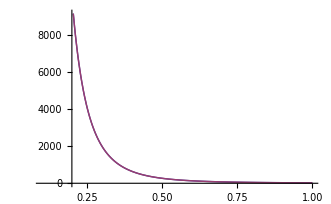

```mathematica
Plot[{(1+Csc[x/2]^4+Sec[x/2]^4),(((3+Cos[x]^2)^2)/((-1+Cos[x]^2)^2))},{x,0.1,Pi/21}]
```

Integrating in the solid angle

## Cross section

```mathematica
σ=Simplify[∫_0.1^1 (dcs/.Me->0)*(E1^2/α^2)*(2π)ⅆct]
```

Integrate::idiv: Integral of \!\(\((3 + ct\^2)\)\^2\/\((\(\(-1\)\) + ct\^2)\)\^2\) does not converge on \!\({0.1`, 1}\).

∫_0.1^1 ((3+ct^2)^2 π)/(2 (-1+ct^2)^2)ⅆct

This is the theoretical value (LAHIRI PAL book : eq 9.36)